1266

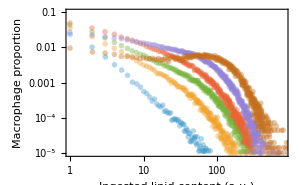

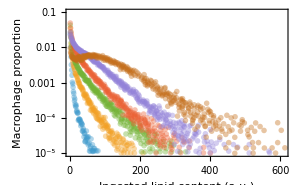

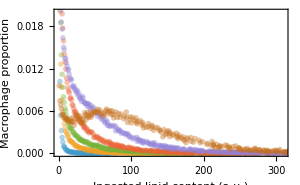

```mathematica
(* resampled experimental data *)
SetDirectory[NotebookDirectory[]];

resamplet0=Join[{{0,1(1-0.05436408687995582)}},Drop[Import["full_initconds.csv","CSV"],1]];
resamplet12=Join[Drop[Import["t12_full.csv"],1]];
resamplet24=Join[Drop[Import["t24_full.csv"],1]];
resamplet36=Join[Drop[Import["t36_full.csv"],1]];
resamplet48=Join[Drop[Import["t48_full.csv"],1]];
resamplet60=Join[Drop[Import["t60_full.csv"],1]];
resamples={resamplet0,resamplet12,resamplet24,resamplet36,resamplet48,resamplet60};

Mdata={{0,1.},{12,0.9762773162434892},{24,0.8759123513425332},{36,0.7481751232867709},{48,0.49635031618480696},{60,0.14233568487147408}};

lipiddata=Drop[Import["avg_LipidContent_data.csv"],1];
lipiddata=Table[{Round[d[[1]]],d[[2]]},{d,lipiddata}];

distributionplot=ListPlot[resamples,PlotRange->{{1,300},{10^(-5),0.01}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (hours)", "Proportion of macrophages"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];
Mplot=ListPlot[Mdata,PlotMarkers->Automatic,PlotTheme->"Scientific",BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Macrophage surviving fraction"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];
Lplot=ListPlot[lipiddata,PlotMarkers->Automatic,PlotTheme->"Scientific",FrameLabel->{"Time t (hours)", "Mean ingested lipid content (a.u.)"},BaseStyle->{FontFamily->"Cambria Math"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];

ndatapoints=Length@resamplet12+Length@resamplet24+Length@resamplet36+Length@resamplet48+Length@resamplet60+(Length@Mdata-1)
{Mplot,Lplot,distributionplot};

opacityval=0.4;
distributionloglogplot=ListLogLogPlot[resamples,PlotRange->{{1,800},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),PlotStyle->{Opacity[opacityval]}]

distributionloglinearplot=ListPlot[resamples,PlotRange->{{1,610},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Log"},PlotStyle->{Opacity[opacityval]}]

distributionlinearplot=ListPlot[resamples,PlotRange->{{0,310},{0,0.02}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Linear"},PlotStyle->{Opacity[opacityval]}]

distributionloglogplot48=ListLogLogPlot[Most@resamples,PlotRange->{{1,500},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),PlotStyle->{Opacity[opacityval]}];

distributionloglinearplot48=ListPlot[Most@resamples,PlotRange->{{1,610},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Log"},PlotStyle->{Opacity[opacityval]}];

distributionlinearplot48=ListPlot[Most@resamples,PlotRange->{{0,310},{0,0.02(*0.02*)}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300,(*PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"},*)ScalingFunctions->{"Linear","Linear"},PlotStyle->{Opacity[opacityval]}];

negbinom[i_,μ_,cv_]:=Module[{r,p},
r=(μ-1)^2/(cv^2*μ^2-μ+1);
p=(μ-1)/(cv^2*μ^2);
Binomial[i+r-2,i-1]*p^r*(1-p)^(i-1)]

decay[i_?IntegerQ,a_,b_]:=Module[{r,p},
k=(*Sum[N@(j)^(-b),{j,1,1000}];*)Zeta[b];
(1/k)*(i)^(-b)
]

logit[x_]:=Log[x/(1-x)];
invlogit[x_]:=1/(1+Exp[-x]);
```

```mathematica
(* Log-likelihood function *)
ClearAll[loglikelihood];

loglikelihood[{e_?NumericQ,μ_?NumericQ,cv_?NumericQ,β0_?NumericQ,β1_?NumericQ,q_?NumericQ,σM_?NumericQ,σL_?NumericQ}]:=
Module[{imax,dx,tmax,n,idx,pmf,βvec,ηvec,fvec,fbar,mInit,eqs,sol,Msol,moutput,Moutput,Loutput,loglikelihoodM,loglikelihoodL,outcome,λ},

rhsVecfunction[v_?VectorQ,βvec_?VectorQ,ηvec_?VectorQ,fvec_?VectorQ,ee_,fbar_,idx_?VectorQ,n_?IntegerQ]:=Module[{betaBar,etaBar,alpha,conv}, (* Here v = (m[0], m[1], ..., m[imax] *)
betaBar=Dot[βvec,v];(* <beta>*)
etaBar=Dot[ηvec,v];(* <Subscript[η, l]>*)
alpha=Dot[βvec*(ee+idx),v]/(fbar*etaBar);(* <beta_i (e+i)> /fbar*)
conv=Prepend[Take[ListConvolve[fvec,ηvec*v,{1,-1},0],n-1],0];(*conv[[i+1]]=Sum_{j=1}^i f_j η_{i-j} m_{i-j} for i>=1*)
alpha (conv-ηvec*v)+(betaBar-βvec)*v
];

imax=1000;
tmax=50;
n=imax+1;
idx=Range[0,imax];


(*βvec=Developer`ToPackedArray@N@(Table[β0,{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp [β1*t],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);*)
βvec=Developer`ToPackedArray@N@(β0+β1*idx);
(*βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx/q])));*)

ηvec=Developer`ToPackedArray@N@(Table[1,{i,1,Length[idx]}]);
(*ηvec=Developer`ToPackedArray@N@(Table[Exp[-q*t],{i,1,Length[idx]}]);*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx]));*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx^2]));*)

fvec=Developer`ToPackedArray@N@(negbinom[#,μ,cv](*decay[#,μ,cv]*)(*pmf[#,λ]*)&/@(idx+1));

mInit=Developer`ToPackedArray@N@PadRight[resamplet0[[All,2]],n,0];
eqs={u'[t]==rhsVecfunction[u[t],βvec,ηvec,fvec,e,μ,idx,n],u[0]==mInit,M'[t]==-M[t] (βvec.u[t]),M[0]==1};

outcome=0;
sol=NDSolve[{eqs,WhenEvent[Total[u[t]]<0.99,"StopIntegration";outcome=1]},{u,M},{t,0,tmax}];

moutput=Table[u[t]/. sol[[1]],{t,{0,12,24,36,48}}];
Moutput=Table[M[t]/. sol[[1]],{t,{0,12,24,36,48}}];
Loutput=Table[idx.(u[t]/. sol[[1]]),{t,{0,12,24,36,48}}];

loglikelihoodM=Sum[-Log[Mdata[[i]][[2]]*(1-Mdata[[i]][[2]])*σM*Sqrt[2 Pi]]-1/(2*σM^2)*(Log[Mdata[[i]][[2]]/(1-Mdata[[i]][[2]])]-Log[Moutput[[i]]/(1-Moutput[[i]])])^2,{i,2,5}];
loglikelihoodL=Sum[-Log[lipiddata[[i]][[2]]*σL*Sqrt[2 Pi]]-1/(2*σL^2)*(Log[lipiddata[[i]][[2]]]-Log[Loutput[[i]]])^2,{i,2,5}];

If[outcome==0&&Element[loglikelihoodM+loglikelihoodL,Reals],loglikelihoodM+loglikelihoodL,-10^(6)]
]


plots[{e_?NumericQ,μ_?NumericQ, cv_?NumericQ,β0_?NumericQ,β1_?NumericQ,q_?NumericQ,σM_?NumericQ,σL_?NumericQ}]:=
Module[{imax,dx,tmax,n,idx,pmf,βvec,ηvec,fvec,fbar,mInit,eqs,sol,Msol,moutput,Moutput,loglikelihoodm,loglikelihoodM,outcome,λ,modeldistributionplot,modelMplot,modelLplot,grid,Loutput,modeldistributionplotloglinear,modeldistributionplotloglog},


rhsVecfunction[v_?VectorQ,βvec_?VectorQ,ηvec_?VectorQ,fvec_?VectorQ,ee_,fbar_,idx_?VectorQ,n_?IntegerQ]:=Module[{betaBar,etaBar,alpha,conv}, (* Here v = (m[0], m[1], ..., m[imax] *)
betaBar=Dot[βvec,v];(* <beta>*)
etaBar=Dot[ηvec,v];(* <Subscript[η, l]>*)
alpha=Dot[βvec*(ee+idx),v]/(fbar*etaBar);(* <beta_i (e+i)> /fbar*)
conv=Prepend[Take[ListConvolve[fvec,ηvec*v,{1,-1},0],n-1],0];(*conv[[i+1]]=Sum_{j=1}^i f_j η_{i-j} m_{i-j} for i>=1*)
alpha (conv-ηvec*v)+(betaBar-βvec)*v
];

imax=1000;
tmax=50;
n=imax+1;
idx=Range[0,imax];

(*βvec=Developer`ToPackedArray@N@(Table[β0,{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp [β1*t],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);*)
βvec=Developer`ToPackedArray@N@(β0+β1*idx);
(*βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx/q])));*)

ηvec=Developer`ToPackedArray@N@(Table[1,{i,1,Length[idx]}]);
(*ηvec=Developer`ToPackedArray@N@(Table[Exp[-q*t],{i,1,Length[idx]}]);*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx]));*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx^2]));*)

fvec=Developer`ToPackedArray@N@(negbinom[#,μ,cv](*decay[#,μ,cv]*)(*pmf[#,λ]*)&/@(idx+1));

mInit=Developer`ToPackedArray@N@PadRight[resamplet0[[All,2]],n,0];

eqs={u'[t]==rhsVecfunction[u[t],βvec,ηvec,fvec,e,μ,idx,n],u[0]==mInit,M'[t]==-M[t] (βvec.u[t]),M[0]==1};

outcome=0;
sol=NDSolve[{eqs,WhenEvent[Total[u[t]]<0.99,"StopIntegration";outcome=1]},{u,M},{t,0,tmax}];

moutput=Table[u[t]/. sol[[1]],{t,{0,12,24,36,48}}];
moutput=Table[Table[{idx[[i]],d[[i]]},{i,1,Length[d]}],{d,moutput}];

modeldistributionplot=ListPlot[moutput,PlotRange->{{0,310},{10^(-5),All}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Linear"}];
modeldistributionplotloglinear=ListPlot[moutput,PlotRange->{{0,1000},{10^(-5),All}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Log"}];
modeldistributionplotloglog=ListPlot[moutput,PlotRange->{{0,800},{10^(-5),All}},ImageSize->300,Joined->True,ScalingFunctions->{"Log","Log"}];


modeldistributionplot=ListPlot[moutput,PlotRange->{{0,300},{0,All}},ImageSize->300,Joined->True];
modelMplot=Plot[{M[t]/. sol[[1]],invlogit[logit[M[t]/. sol[[1]]]+Quantile[NormalDistribution[0,σM],0.025]],invlogit[logit[M[t]/. sol[[1]]]+Quantile[NormalDistribution[0,σM],0.975]]},{t,0,60},PlotRange->{{-0.5,50},{-0.05,1.05}},PlotStyle->{Automatic,{Dashed,Thin,Opacity[0]},{Dashed,Thin,Opacity[0]}},Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.1],ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time \!\(\*StyleBox[\"t\",FontSlant->\"Italic\"]\)\!\(\*StyleBox[\" \",FontSlant->\"Italic\"]\)(hours)","Cell population M̂"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];
modelLplot=Plot[{idx.(u[t]/. sol[[1]]),(idx.(u[t]/. sol[[1]]))*Quantile[LogNormalDistribution[0,σL],0.025],(idx.(u[t]/. sol[[1]]))*Quantile[LogNormalDistribution[0,σL],0.975]},{t,0,50},PlotRange->{{-0.5,50},{-0.05,50}},PlotStyle->{Automatic,{White,Dashed,Thin,Opacity[0]},{White,Dashed,Thin,Opacity[0]}},Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.1],ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Mean ingested lipid (L̂)_M (a.u.)"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];


Grid[{{Show[modelMplot,Mplot],Show[modelLplot,Lplot]},{Show[distributionlinearplot48,modeldistributionplot],Show[distributionloglinearplot48,modeldistributionplotloglinear](*,Show[distributionloglogplot48,modeldistributionplotloglog]*)}}]
]
```

```mathematica
(* MLE: β = β0 *)
nstep=1;
{eval,μval,cvval,β0val,σMval,σmval}={0.5247271075459354,0.16267772772806782,1.2,0.006887368250625402,0.8051512190343388,0.4746218889136089};
NMaximize[{loglikelihood[{100*e,100*μ,cvval,β0,0,1,σM,σm}],0.01<e<1,0.01<μ<1, 0.001<β0<1,0.01<σM<1,0.01<σm<1},{e,μ,β0,σM,σm},Method->{Automatic,"InitialPoints"->{{eval,μval,β0val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,μ,β0,σM,σm},loglikelihood[{100*e,100*μ,cvval,β0,0,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.524727,0.162678,0.00688737,0.805151,0.474622},-8.03005}

Current x: {{0.52444,0.353754,0.00688788,0.805685,0.474702},-8.03003}

{-8.03004,{e→0.524477,μ→0.162691,β0→0.00688753,σM→0.805671,σm→0.474707}}

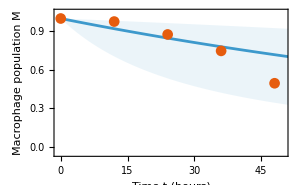
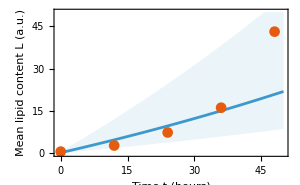
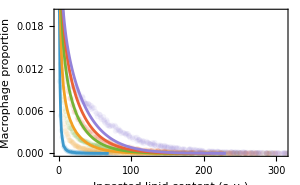
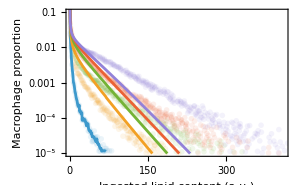
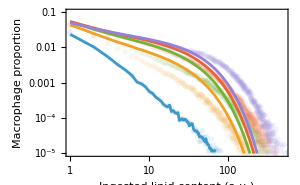
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots[{100*e,100*μ,cvval,β0,0,1,σM,σL}/.{e->0.5244768105360409,μ->0.16269056385716366,β0->0.006887528830896541,σM->0.8056711399927171,σL->0.4747070567058283}]
```

```mathematica
(* MLE: β = β0*Exp [β1*t] *)
nstep=1;
{eval,μval,cvval,β0val,β1val,σMval,σmval}={0.5286062183817707,0.1455088428748961,1.9993747328174223,0.15872415807247975,0.07345566803880664,0.3,0.3};
NMaximize[{loglikelihood[{100*e,100*μ,cvval,β0/100,β1,1,σM,σm}],0.1<e<1,0.01<μ<1,0.01<β0<0.3,0.01<β1<0.3,0.01<σM<1,0.01<σm<1},{e,μ,β0,β1,σM,σm},Method->{Automatic,"InitialPoints"->{{eval,μval,β0val,β1val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,μ,β0,β1,σM,σm},loglikelihood[{100*e,100*μ,cvval,β0/100,β1,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.613611,0.199032,0.225602,0.0550448,0.336624,0.119385},2.56558}

Current x: {{0.590777,0.17889,0.232284,0.0540085,0.300481,0.0539246},4.12698}

Current x: {{0.564152,0.181887,0.247142,0.0531113,0.298659,0.0522903},4.18964}

Current x: {{0.551991,0.200454,0.250994,0.0530539,0.329378,0.0534513},4.26201}

Current x: {{0.550621,0.201149,0.251734,0.0530148,0.33024,0.0535865},4.2622}

{4.26248,{e→0.550582,μ→0.135314,β0→0.251757,β1→0.0530123,σM→0.330339,σm→0.0535777}}

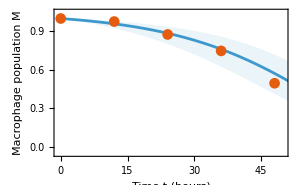
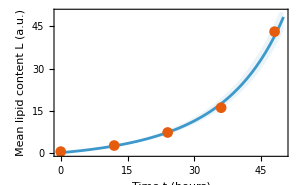
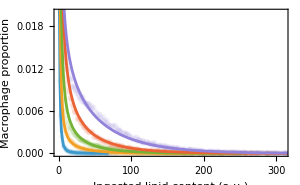
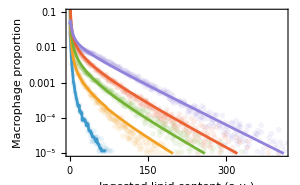
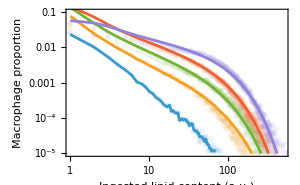
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots[{100*e,100*μ,cvval,β0/100,β1,1,σM,σm}/.{e->0.5505815431845544,μ->0.13531416178478767,β0->0.2517566243136555,β1->0.05301231155780243,σM->0.3303393676957174,σm->0.053577747986256544}]
```

```mathematica
(* β = β0 + β1*idx *)
nstep=1;
{eval,μval,cvval,β0val,β1val,σMval,σmval}={0.431,0.363,0.89,0.33,0.1,0.5,0.5};
FindMaximum[{loglikelihood[{100*e,100*μ,cv,β0/100,β1/100,1,σM,σm}],0.01<e<1,0.01<μ<1,0.1<cv<3,0.001<β0<1,0.001<β1<1,0.01<σM<1,0.01<σm<1},{{e,eval},{μ,μval},{cv,cvval},{β0,β0val},{β1,β1val},{σM,σMval},{σm,σmval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{e,μ,cv,β0,β1,σM,σm},loglikelihood[{100*e,100*μ,cv,β0/100,β1/100,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

```mathematica
{eval,μval,cvval,β0val,β1val,σMval,σLval}={0.4928167424352051,0.4520713693163495,1.2011557241092925,0.2860289699563494,0.08872108823291569,0.37144311719070766,0.027628733791762956};
NMaximize[{loglikelihood[{100*e,100*μ,cv,β0/100,β1/100,1,σM,σL}],0.01<e<1,0.01<μ<1,0.1<cv<3,0.01<β0<1,0.01<β1<0.3,0.01<σM<1,0.01<σL<1},{e,μ,cv,β0,β1,σM,σL},Method->{Automatic,"InitialPoints"->{{eval,μval,cvval,β0val,β1val,σMval,σLval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,μ,cv,β0,σM,σL},loglikelihood[{100*e,100*μ,cv,β0/100,β1/100,1,σM,σL}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.492817,0.452071,1.20116,0.286029,0.371443,0.0276287},6.44657}

Current x: {{0.492817,0.452071,1.20116,0.286029,0.371443,0.0276287},6.44657}

Current x: {{0.492817,0.452071,1.20116,0.286029,0.371443,0.0276287},6.44657}

{6.44657,{e→0.492817,μ→0.452071,cv→1.20116,β0→0.286029,β1→0.0887211,σM→0.371443,σL→0.0276287}}

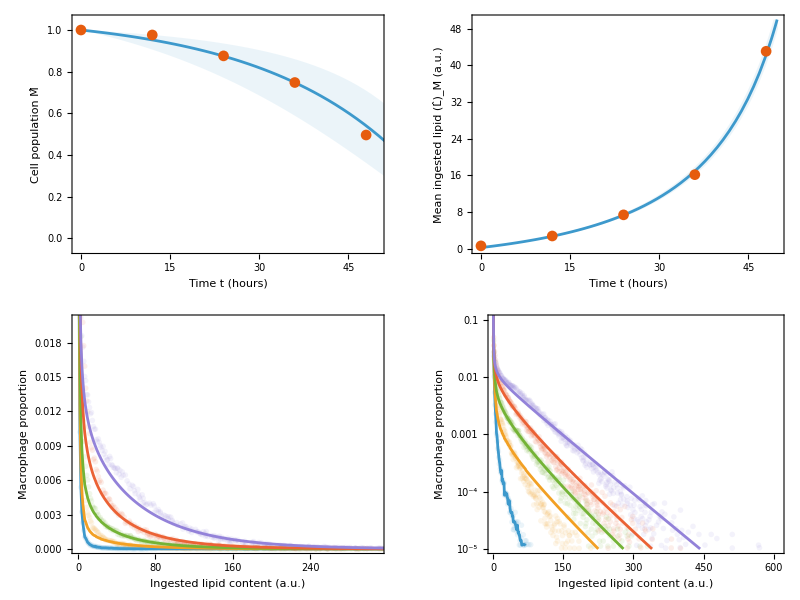

```mathematica
plots[{100*e,100*μ,cv,β0/100,β1/100,1,σM,σL}/.{e->0.49281674243589124,μ->0.45207136931273595,cv->1.2011557241079742,β0->0.2860289699564961,β1->0.08872108822916311,σM->0.3714431171861786,σL->0.027628733782485183}]
```

```mathematica
(* β=β1/(1+(β1-β0)/β0*Exp[-t/q]):Saturating time-dependent death rate. Tends to β1 -> infinity! *)
nstep=1;
{eval,μval,cvval,β0val,β1val,qval,σMval,σmval}={0.5601537795500029,0.1280699474372899,1.2,0.2365398918610906,9.999878647455771,16.909306408890235,0.3233046059688394,0.06679059940417201};
FindMaximum[{loglikelihood[{100*e,100*μ,cvval,β0/100,β1/100,q,σM,σm}],0.1<e<1,0.01<μ<1,0.01<β0<1,0.01<β1<1000,0.1<q<100,0.01<σM<1,0.01<σm<1},{{e,eval},{μ,μval},{β0,β0val},{β1,β1val},{q,qval},{σM,σMval},{σm,σmval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{e,μ,β0,β1,q,σM,σm},loglikelihood[{100*e,100*μ,cvval,β0/100,β1/100,q,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.560154,0.12807,0.23654,9.99988,16.9093,0.323305,0.0667906},3.46692}

Current x: {{0.558549,0.206891,0.237978,10.7283,17.0452,0.325747,0.0666996},3.51861}

Current x: {{0.554235,0.42559,0.245463,16.234,17.9663,0.329275,0.0599133},3.63111}

Current x: {{0.552318,0.486796,0.245486,19.3543,17.8688,0.328319,0.0587297},3.84244}

Current x: {{0.551921,0.49653,0.248561,29.0121,18.3598,0.330908,0.0575661},3.93676}

Current x: {{0.550919,0.496075,0.249013,37.063,18.3757,0.330807,0.0568284},4.04022}

Current x: {{0.550642,0.49739,0.250335,54.6144,18.5914,0.331785,0.056086},4.10058}

Current x: {{0.550124,0.497291,0.250927,77.6203,18.6618,0.332011,0.0555055},4.15252}

Current x: {{0.54992,0.497094,0.25147,117.196,18.747,0.33235,0.0550827},4.18768}

Current x: {{0.54969,0.496918,0.251852,184.888,18.8004,0.332543,0.0547466},4.21433}

Current x: {{0.549621,0.496887,0.252016,291.927,18.8265,0.332636,0.0545978},4.23179}

Current x: {{0.549614,0.496718,0.252091,448.68,18.84,0.332684,0.0545318},4.24213}

Current x: {{0.549668,0.496665,0.252042,533.563,18.8355,0.332665,0.0545684},4.24524}

Current x: {{0.550553,0.490563,0.251586,559.509,18.829,0.330679,0.053949},4.24706}

Current x: {{0.5507,0.466019,0.251541,653.169,18.8338,0.33029,0.0537892},4.24922}

Current x: {{0.550661,0.418141,0.251587,791.06,18.8396,0.330317,0.053753},4.25171}

Current x: {{0.550665,0.411468,0.251586,818.478,18.8394,0.330318,0.053753},4.25208}

Current x: {{0.550678,0.391349,0.251594,915.041,18.8421,0.330265,0.0537146},4.25322}

Current x: {{0.550673,0.359512,0.251603,976.332,18.8433,0.330269,0.0537063},4.2538}

Current x: {{0.550672,0.364922,0.251604,982.612,18.8434,0.33027,0.0537063},4.25385}

Current x: {{0.550672,0.360769,0.251605,998.883,18.8437,0.330268,0.0537032},4.25398}

Current x: {{0.550672,0.360369,0.251606,999.774,18.8437,0.330268,0.0537031},4.25399}

{4.25399,{e→0.550672,μ→0.360369,β0→0.251606,β1→999.774,q→18.8437,σM→0.330268,σm→0.0537031}}

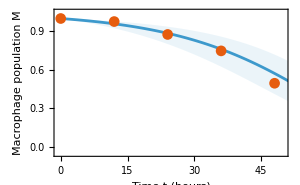
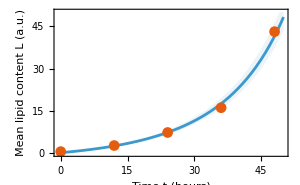
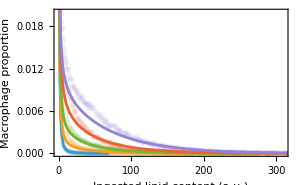
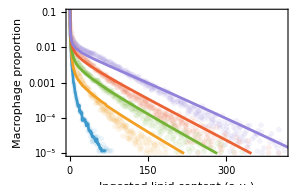
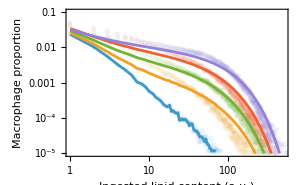
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots[{100*e,100*μ,cvval,β0/100,β1/100,q,σM,σm}/.{e->0.5506722189201272,μ->0.36036899076454953,β0->0.25160555286543246,β1->999.7740468082359,q->18.84369697471049,σM->0.33026805586022606,σm->0.053703120435647275}]
```

```mathematica
(* β = β0+(β1-β0)*(1-Exp[-idx/q]: Saturating lipid-dependent death rate *)
nstep=1;
{eval,μval,cvval,β0val,β1val,qval,σMval,σmval}={0.5789979830209905,0.09930430409569022,2.367914552261123,0.01000051165458577,0.03202540582994149,2.3003450111156925,0.5,0.5};
FindMaximum[{loglikelihood[{100*e,100*μ,cv,β0/100,β1,q,σM,σm}],0.1<e<1,0.01<μ<1,0.1<cv<3,0.001<β0<1,0.01<β1<1,0.1<q<100,0.01<σM<1,0.01<σm<1},{{e,eval},{μ,μval},{cv,cvval},{β0,β0val},{β1,β1val},{q,qval},{σM,σMval},{σm,σmval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{e,μ,cv,β0,β1,q,σM,σm},loglikelihood[{100*e,100*μ,cv,β0/100,β1,q,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.606322,0.953382,1.72422,0.0119976,0.124073,3.60866,0.33658,0.0300315},6.54489}

Current x: {{0.606322,0.953382,1.72422,0.0119976,0.124073,3.60866,0.33658,0.0300315},6.54489}

$Aborted

```mathematica
nstep=1;
{eval,μval,cvval,β0val,β1val,qval,σMval,σLval}={0.6063216714398263,0.9533824089677247,1.7242235674264272,0.011997585659707932,0.12407263295710909,3.6086573999772424,0.33657988693564966,0.030031517970123375};
NMaximize[{loglikelihood[{100*e,100*μ,cv,β0/100,β1,q,σM,σL}],0.1<e<1,0.01<μ<1,0.1<cv<3,0.001<β0<0.05,0.01<β1<0.3,0.1<q<100,0.01<σM<1,0.01<σL<1},{e,μ,cv,β0,β1,q,σM,σL},Method->{Automatic,"InitialPoints"->{{eval,μval,cvval,β0val,β1val,qval,σMval,σLval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,μ,cv,β0,σM,σL},loglikelihood[{100*e,100*μ,cv,β0/100,β1,q,σM,σL}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.606322,0.953382,1.72422,0.0119976,0.33658,0.0300315},6.54489}

Current x: {{0.606322,0.953382,1.72422,0.0119976,0.33658,0.0300315},6.54489}

Current x: {{0.606225,0.954053,1.72326,0.0120465,0.336828,0.0297111},6.54541}

Current x: {{0.606025,0.955516,1.7223,0.0121262,0.337736,0.0298452},6.54633}

Current x: {{0.605425,0.963073,1.71154,0.0126991,0.343452,0.0296812},6.5494}

{6.55517,{e→0.605145,μ→0.971811,cv→1.69994,β0→0.0121205,β1→0.12616,q→3.71033,σM→0.349052,σL→0.0297787}}

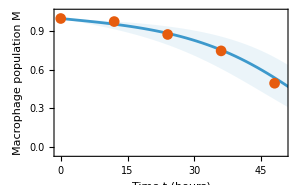
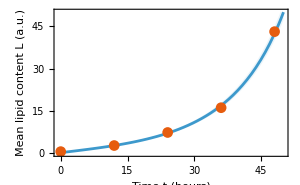
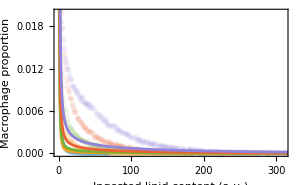
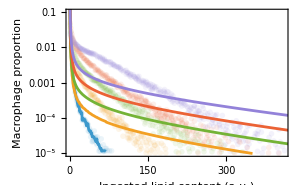
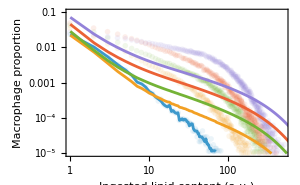
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots[{100*e,100*μ,cv,β0/100,β1,q,σM,σL}/.{e->0.6051450680766605,μ->0.9718107678066824,cv->1.699935971733837,β0->0.012120480600237278,β1->0.12615978240960543,q->3.7103271897856294,σM->0.34905160520616924,σL->0.02977870132128002}]
```